```mathematica
Quit[]
```

## Load Packages

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities

### Functions for generating diagrams

```mathematica
exclusions={V[1],V[2]};

frModelName="EFT_MeV_DM_scalar";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateρ=V[2];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];
states=S[7];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Three body phase space bounds

```mathematica
getTBounds[s_,m1_,m2_,m3_,M_]:=Module[{E1,E2,t,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getSBounds⟦1⟧<s<getSBounds⟦2⟧}];
(* energies *)
E1=  (M^2+m1^2-s)/(2M);
E2= (M^2+m2^2-t)/(2M);
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,t]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}
]

getSBounds[m1_,m2_,m3_,M_]:={(m2+m3)^2,(M-m1)^2};


getYBounds[x_,m1_,m2_,m3_,M_]:=Module[{E1,E2,y,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getXBounds⟦1⟧<x<getXBounds⟦2⟧}];
(* energies *)
E1=  M x/ 2;
E2= M y/ 2;
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,y]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}]


getXBounds[m1_,m2_,m3_,M_]:={(M^2-(M-m1)^2+m1^2)/M^2,(M^2-(m2+m3)^2+m1^2)/M^2};
```

## S→ l̄ l

### Set Scalar Products

```mathematica
SP[pl,pl]=(μl*ms)^2;
SP[plbar,plbar]=(μl*ms)^2;
SP[k,k]=0;

SP[pl,plbar]=1/2(ms^2-(μl*ms)^2-(μl*ms)^2);
```

### Compute Msqrd

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{states},{statel,statelbar}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {ps},
OutgoingMomenta-> {pl,plbar},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//Contract//ReplaceAll[#,ml-> μl*ms]&;
ampConj = ComplexConjugate[sllbar`amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd=ampConj*amp//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&;
sllbar`msqrd=msqrd//Simplify
]
```

-(2 gsff^2 μl^2 (2 μl-1) (2 μl+1) ms^4)/vh^2

### Compute Decay Width

```mathematica
sllbar`Γ=1/(2ms)(4π)/(16 π^2)((√(1-4 μl^2))/2)sllbar`msqrd//FullSimplify
```

(gsff^2 μl^2 (1-4 μl^2)^(3/2) ms^3)/(8 π vh^2)

## S→ l̄ l γ

### Compute Matrix element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
SP[pl,pl]=(μl*ms)^2;
SP[plbar,plbar]=(μl*ms)^2;
SP[k,k]=0;

SP[pl,plbar]=1/2(s-(μl*ms)^2-(μl*ms)^2);
SP[k,plbar]=1/2(t-0-(μl*ms)^2);
SP[k,pl]=1/2(u-0-(μl*ms)^2);
```

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{states},{statel,statelbar,stateγ}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {ps},
OutgoingMomenta-> {pl,plbar,k},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//Contract//ReplaceAll[#,ml-> μl*ms]&;
ampConj=ComplexConjugate[amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd = amp*ampConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&;
msqrd = msqrd//DoPolarizationSums[#,k,0]&//Simplify;
sllbarγ`msqrd=msqrd]
```

(4 gsff^2 μl^2 ms^2 qe^2 (2 s^2 (t-μl^2 ms^2) (u-μl^2 ms^2)+(-2 μl^2 ms^2+t+u)^2 (13 μl^4 ms^4+t (u-3 μl^2 ms^2)-3 μl^2 ms^2 u)+2 s (-10 μl^6 ms^6+11 μl^4 ms^4 u+t^2 (u-2 μl^2 ms^2)-2 μl^2 ms^2 u^2+t (11 μl^4 ms^4-10 μl^2 ms^2 u+u^2))))/(vh^2 (t-μl^2 ms^2)^2 (u-μl^2 ms^2)^2)

### Convert to x and y

```mathematica
sllbarγ`dΓdsdt=(1/(2ms))(1/(16 ms^2(2π)^3))sllbarγ`msqrd//ReplaceAll[#,u-> ms^2+2 ms^2 μl^2-s-t]&//Simplify;
sllbarγ`dΓdxdy=ms^4 sllbarγ`dΓdsdt//ReplaceAll[#,{s-> ms^2(1-x),t-> ms^2(1-y+μl^2)}]&//Simplify;
```

```mathematica
sllbarγ`dΓdxdy`dynamic=sllbarγ`dΓdxdy//SelectNotFree[#,y]&;
sllbarγ`dΓdxdy`coeff=sllbarγ`dΓdxdy//SelectFree[#,y]&;
```

```mathematica
sllbarγ`dΓdxdy`dynamic*sllbarγ`dΓdxdy`coeff-sllbarγ`dΓdxdy
```

0

### Compute y integral

Part::partd: Part specification getXBounds⟦1⟧ is longer than depth of object.

Part::partd: Part specification getXBounds⟦2⟧ is longer than depth of object.

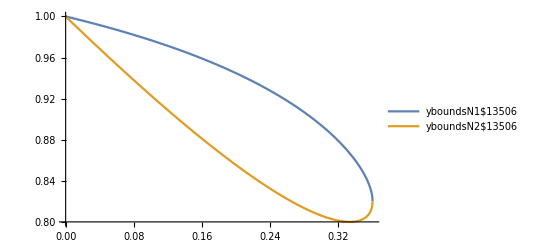

```mathematica
ybounds = getYBounds[x,0,μl*ms,μl*ms,ms]//Simplify;
xbounds=getXBounds[0,μl*ms,μl*ms,ms]//Simplify;

Module[{yboundsN1,yboundsN2,xboundsN1,xboundsN2},
(* test which curve is the upper and which is lower *)
yboundsN1=ybounds⟦1⟧/.{μl-> 0.4,ms->1};
yboundsN2=ybounds⟦2⟧/.{μl-> 0.4,ms->1};
xboundsN1=xbounds⟦1⟧/.{μl-> 0.4,ms->1};
xboundsN2=xbounds⟦2⟧/.{μl-> 0.4,ms->1};
Plot[{yboundsN1,yboundsN2},{x,xboundsN1,xboundsN2},PlotLegends->"Expressions"]
]
```

```mathematica
Module[{integral,lim1,lim2,result},
$Assumptions={xbounds⟦1⟧<x<xbounds⟦2⟧,μl>0};
integral=Integrate[sllbarγ`dΓdxdy`dynamic,y]//Simplify;
lim1=integral/.{y-> ybounds⟦1⟧};
lim2=integral/.{y-> ybounds⟦2⟧};
$Assumptions=True;
sllbarγ`dΓdx`dynamic=lim1-lim2//Simplify
]
```

1/x(-(16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log((x (-√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))-(16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log((x (√(x-1) √(4 μl^2+x-1)-x+1))/(2 (x-1)))+(16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log(-(x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))+(16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log((x (√(x-1) √(4 μl^2+x-1)+x-1))/(2 (x-1)))-4 (4 μl^2-1) √(x-1) √(4 μl^2+x-1))

```mathematica
sllbarγ`dΓdx`dynamic//SelectNotFree[#,Log[__]]&//SelectNotFree[#,Log[__]]&//StandardForm
```

-(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[(x (-1+x-√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]-(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[(x (1-x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]+(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]+(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[(x (-1+x+√(-1+x) √(-1+x+4 μl^2)))/(2 (-1+x))]

Simply logs by hand

```mathematica
+(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[(x (-1+x-√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x))]
+(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[(x (1-x+√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x))]
-(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[-(x (-1+x+√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x))]
-(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[(x (-1+x+√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x))]
```

```mathematica
(((x (-1+x-√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x)))/1)(((x (1-x+√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x)))/1)(1/(-(x (-1+x+√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x))))(1/((x (-1+x+√((-1+x) (-1+x+4 μl^2))))/(2 (-1+x))))//Simplify//StandardForm
```

((1-x+√((-1+x) (-1+x+4 μl^2)))^2)/((-1+x+√((-1+x) (-1+x+4 μl^2)))^2)

Compute put logs back in

```mathematica
sllbarγ`dΓdx`dynamic=1/x(-4 √(-1+x) (-1+4 μl^2) √(-1+x+4 μl^2)+(2-2 x+x^2-12 μl^2+8 x μl^2+16 μl^4) Log[((1-x+√((-1+x) (-1+x+4 μl^2)))^2)/((-1+x+√((-1+x) (-1+x+4 μl^2)))^2)])
```

((16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log(((√((x-1) (4 μl^2+x-1))-x+1)^2)/((√((x-1) (4 μl^2+x-1))+x-1)^2))-4 (4 μl^2-1) √(x-1) √(4 μl^2+x-1))/x

### Compute Spectrum

```mathematica
sllbarγ`dndx=sllbarγ`dΓdx`dynamic*sllbarγ`dΓdxdy`coeff/sllbar`Γ
```

(qe^2 ((16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log(((√((x-1) (4 μl^2+x-1))-x+1)^2)/((√((x-1) (4 μl^2+x-1))+x-1)^2))-4 (4 μl^2-1) √(x-1) √(4 μl^2+x-1)))/(8 π^2 (1-4 μl^2)^(3/2) x)

```mathematica
sllbarγ`dΓdx`dynamic/.{μl-> mul}//FortranForm
```

(-4*(-1 + 4*mul**2)*Sqrt(-1 + x)*Sqrt(-1 + 4*mul**2 + x) + (2 - 12*mul**2 + 16*mul**4 - 2*x + 8*mul**2*x + x**2)*
     -     Log((1 - x + Sqrt((-1 + x)*(-1 + 4*mul**2 + x)))**2/(-1 + x + Sqrt((-1 + x)*(-1 + 4*mul**2 + x)))**2))/x

```mathematica
sllbarγ`dΓdxdy`coeff/sllbar`Γ/.{μl-> mul}//FortranForm
```

qe**2/(8.*(1 - 4*mul**2)**1.5*Pi**2)

```mathematica
sllbarγ`dndx
```

(qe^2 ((16 μl^4-12 μl^2+x^2+8 μl^2 x-2 x+2) log(((√((x-1) (4 μl^2+x-1))-x+1)^2)/((√((x-1) (4 μl^2+x-1))+x-1)^2))-4 (4 μl^2-1) √(x-1) √(4 μl^2+x-1)))/(8 π^2 (1-4 μl^2)^(3/2) x)

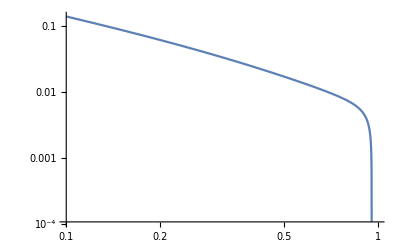

```mathematica
LogLogPlot[sllbarγ`dndx/.{μl-> 0.105,qe-> (4Pi/137.)^(1/2)},{x,0.1,1}]
```